```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]];
```

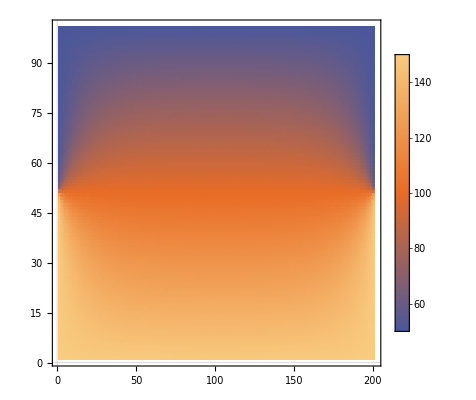

```mathematica
data = Import["cmake-build-release/temp.txt","Table"];
ListDensityPlot[data,PlotTheme->"Scientific",PlotRange->Full]
```

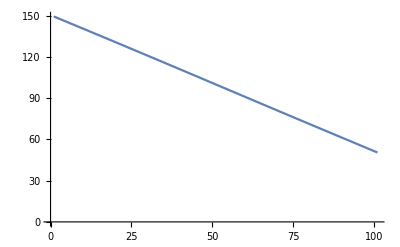

```mathematica
ListLinePlot@data[[;;,100]]
```